# Homework assignment 8

Kyle McGraw <kmcgraw@caltech.edu>, Partners: Allison Glynn, Dallas Taylor
Free extension used on this assignment.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorSSA.m"]
```

```mathematica
Attributes[rxno]=HoldAll;
rxno[2a_,c_+d_,k_]:=rxnl[{a,a},{c,d},k]
rxno[a_+b_,2c_,k_]:=rxnl[{a,b},{c,c},k]
rxno[2a_,2c_,k_]:=rxnl[{a,a},{c,x},k]
rxno[a_+b_,c_+d_,k_]:=rxnl[{a,b},{c,d},k]
rxno[a_,b_,k_]:=rxnl[{a},{b},k]
```

```mathematica
HaltedSurfaceCRNQ[crn_List,state_List]:= Module[{l,m,n,unirules,birules,S,ExistsReactionQ},
Switch[Length[Dimensions[state]],1,S = {{state}},2,S={state},3,S=state];
{l,m,n}=Dimensions[S];
birules=Cases[crn/.{rxnl[{a_,b_},{c_,d_},k_]:>({a,b}->{c,d,k})},_Rule];
unirules=Cases[crn/.{rxnl[{a_},{b_},k_]:>({a}->{b,k})},_Rule];
ExistsReactionQ[{i_,j_,k_}]:=(Length[Join[
ReplaceList[{S[[i,j,k]]},unirules],
If[i<l,ReplaceList[{S[[i,j,k]],S[[i+1,j,k]]},birules],{}],
If[i>1,ReplaceList[{S[[i,j,k]],S[[i-1,j,k]]},birules],{}],
If[j<m,ReplaceList[{S[[i,j,k]],S[[i,j+1,k]]},birules],{}],
If[j>1,ReplaceList[{S[[i,j,k]],S[[i,j-1,k]]},birules],{}],
If[k<n,ReplaceList[{S[[i,j,k]],S[[i,j,k+1]]},birules],{}],
If[k>1,ReplaceList[{S[[i,j,k]],S[[i,j,k-1]]},birules],{}]
]]>0);
!AnyTrue[Tuples[{Range[l],Range[m],Range[n]}],ExistsReactionQ]
]
```

```mathematica
InfoRunSurfaceCRN[crn_List,state_List,tmax_,haltcheck_:True]:= Module[{l,m,n,species,count=0,t=0,kmax,unirules,birules,S,dirs,i,j,k,di,dj,dk,actions,new1,new2,ktot,balance},
If[Count[crn,_conc|_rxn]=!=0 || Length[Cases[crn,Except[rxnl[{_,_},{_,_},_]|rxnl[{_},{_},_]]]]>0,
Return["conc and rxn statements not allowed. 1-1 and 2-2 rxnl only."]];
Switch[Length[Dimensions[state]],
1,S = {{state}}; dirs={{0,0,-1},{0,0,+1}},
2,S={state}; dirs={{0,-1,0},{0,+1,0},{0,0,-1},{0,0,+1}},
3,S=state; dirs={{0,-1,0},{0,+1,0},{0,0,-1},{0,0,+1},{-1,0,0},{+1,0,0}}
];
{l,m,n}=Dimensions[S];balance=(1+Length[dirs]);
birules=Cases[crn/.{rxnl[{a_,b_},{c_,d_},k_]:>({a,b}->{c,d,k})},_Rule];
unirules=Cases[crn/.{rxnl[{a_},{b_},k_]:>({a}->{b,k})},_Rule];
species=SpeciesInRxnsys[crn];
kmax=Max[Total[Last/@Last/@#]&/@GatherBy[unirules~Join~birules,First]];
While[t<tmax,
t+=-Log[RandomReal[]]/(balance kmax l m n); If[t>tmax,Break[]];
{i,j,k}={RandomInteger[{1,l}],RandomInteger[{1,m}],RandomInteger[{1,n}]};
If[RandomReal[]<1/balance,(* unimolecular rate should be balanced with the bimolecular rates *)
actions=ReplaceList[{S[[i,j,k]]},unirules];ktot=Total[Last/@actions];
If[Length[actions]>0&&ktot>0,
new1=RandomChoice[(Last/@actions)->(First/@actions)];
If[RandomReal[]<ktot/kmax,S[[i,j,k]]=new1];count++],
(* else bimolecular *)
{di,dj,dk}=RandomChoice[dirs];
If[1≤i+di≤l&&1≤j+dj≤m&&1≤k+dk≤n,
actions=ReplaceList[{S[[i,j,k]],S[[i+di,j+dj,k+dk]]},birules];ktot=Total[Last/@actions];
If[Length[actions]>0&&ktot>0,
{new1,new2}=RandomChoice[(Last/@actions)->(Take[#,2]&/@actions)];If[RandomReal[]<ktot/kmax,{S[[i,j,k]],S[[i+di,j+dj,k+dk]]}={new1,new2};count++]]
];
];
];
{{tmax,count,If[haltcheck,HaltedSurfaceCRNQ[crn,S],None]},
Switch[Length[Dimensions[state]],1,First[First[S]],2,First[S],3,S]}
]
```

```mathematica
RunSurfaceCRN[crn_List,state_List,tmax_]:= Last[InfoRunSurfaceCRN[crn,state,tmax,False]]
```

## Part 1: Well-mixed and surface CRNs that solve graph coloring problems by stochastic local search.

(a).  Given k>1 and an arbitrary connected graph G=(V,E), construct a well-mixed stochastic CRN that is guaranteed to halt with a solution to the k-coloring problem if one exists (and will run forever otherwise).   The graph G has vertices V and undirected edges E.  A k-coloring is a map from V to {1,..., k} such that no two adjacent vertices have the same color.  Four example graphs are given; the example coloring for G1 is valid, the example coloring for G2 is invalid,  the randomly-chosen one for G3 is probably invalid, and the example coloring for G4 is valid.  Your CRN should have no more than O(k|E|) reactions.  Feel free to demonstrate success on graphs other than the ones below.

Technical note:  I encountered a bug when using Table[ ] and Do[ ] with graphs where the vertices are represented as symbols.  So I advise representing vertices as either integers or strings.

We create a reactions for every edge if they are the same color, change one of the vertices to either the color above or below (colors represented as numbers). This means that we will keep doing reactions until no adjacent vertices have the same color.

For each example, I showed what k they are not colorable at, then what k they are colorable at. I used the coloring found to recolor the graph.

```mathematica
Clear[k,G]
```

```mathematica
GraphColorSolution1[k_,G_]:= Module[{tmax=300,coloring,trajectory},
coloring=Flatten[Table[Table[{rxno[Symbol[EdgeList[G][[j,1]]<>ToString@i]+Symbol[EdgeList[G][[j,2]]<>ToString@i],Symbol[EdgeList[G][[j,1]]<>ToString@i]+Symbol[EdgeList[G][[j,2]]<>ToString@(Mod[i,k]+1)],1],rxno[Symbol[EdgeList[G][[j,1]]<>ToString@i]+Symbol[EdgeList[G][[j,2]]<>ToString@i],Symbol[EdgeList[G][[j,1]]<>ToString@i]+Symbol[EdgeList[G][[j,2]]<>ToString@(If[i==1,k,i-1])],1]},{j,1,Length[EdgeList[G]]}],{i,1,k}]];
trajectory=SimulateRxnsysSSA[Join[coloring,Table[conc[Symbol[VertexList[G][[j]]<>ToString@1],1],{j,1,Length[VertexList[G]]}]],tmax];
CellPrint[{ListLinePlot[trajectory,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[coloring]],{Flatten[Table[Table[Symbol[VertexList[G][[j]]<>ToString@i],{i,1,k}],{j,1,Length[VertexList[G]]}]],trajectory["Values"][[-1]]}//MatrixForm}]
]
```

```mathematica
GraphColorSolution2[k_,G_]:= Module[{tmax=300,coloring,trajectory},
coloring=Flatten[Table[Table[{rxno[Symbol[FromLetterNumber[EdgeList[G][[j,1]]]<>ToString@i]+Symbol[FromLetterNumber[EdgeList[G][[j,2]]]<>ToString@i],Symbol[FromLetterNumber[EdgeList[G][[j,1]]]<>ToString@i]+Symbol[FromLetterNumber[EdgeList[G][[j,2]]]<>ToString@(Mod[i,k]+1)],1],rxno[Symbol[FromLetterNumber[EdgeList[G][[j,1]]]<>ToString@i]+Symbol[FromLetterNumber[EdgeList[G][[j,2]]]<>ToString@i],Symbol[FromLetterNumber[EdgeList[G][[j,1]]]<>ToString@i]+Symbol[FromLetterNumber[EdgeList[G][[j,2]]]<>ToString@(If[i==1,k,i-1])],1]},{j,1,Length[EdgeList[G]]}],{i,1,k}]];
trajectory=SimulateRxnsysSSA[Join[coloring,Table[conc[Symbol[FromLetterNumber[VertexList[G][[j]]]<>ToString@1],1],{j,1,Length[VertexList[G]]}]],tmax];
CellPrint[{ListLinePlot[trajectory,PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[coloring]],{Flatten[Table[Table[Symbol[FromLetterNumber[VertexList[G][[j]]]<>ToString@i],{i,1,k}],{j,1,Length[VertexList[G]]}]],trajectory["Values"][[-1]]}//MatrixForm}]
]
```

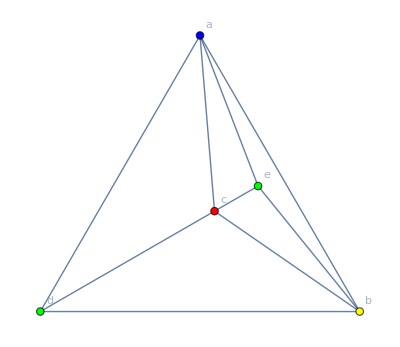

```mathematica
G1 = Graph[{"a","b","c","d","e"},{"a"<->"b","a"<->"c","a"<->"d","a"<->"e","b"<->"c","b"<->"d","b"<->"e","c"<->"d","c"<->"e"}];
PlanarGraph[G1,VertexLabels->Automatic,VertexStyle->{"a"->Blue,"b"->Yellow,"c"->Red,"d"->Green,"e"->Green}]
```

```mathematica
GraphColorSolution1[3,G1]
```

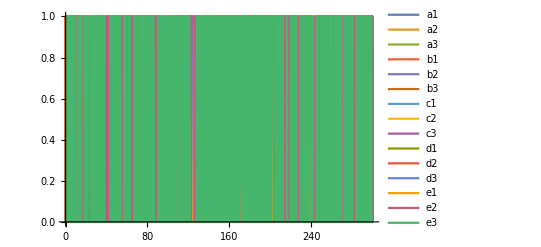

(a1 | a2 | a3 | b1 | b2 | b3 | c1 | c2 | c3 | d1 | d2 | d3 | e1 | e2 | e3
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0)

```mathematica
GraphColorSolution1[4,G1]
```

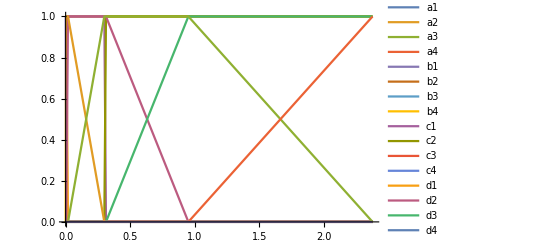

(a1 | a2 | a3 | a4 | b1 | b2 | b3 | b4 | c1 | c2 | c3 | c4 | d1 | d2 | d3 | d4 | e1 | e2 | e3 | e4
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0)

```mathematica
PlanarGraph[G1,VertexLabels->Automatic,VertexStyle->{"a"->Blue,"b"->Yellow,"c"->Red,"d"->Green,"e"->Green}]
```

-Graphics-

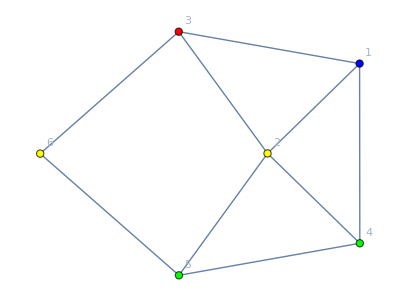

```mathematica
G2=Graph[{1,2,3,4,5,6},{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->6,4<->5,5<->6}];
Graph[G2,VertexLabels->Automatic,VertexStyle->{1->Blue,2->Yellow,3->Red,4->Green,5->Green,6->Yellow}]
```

```mathematica
GraphColorSolution2[2,G2]
```

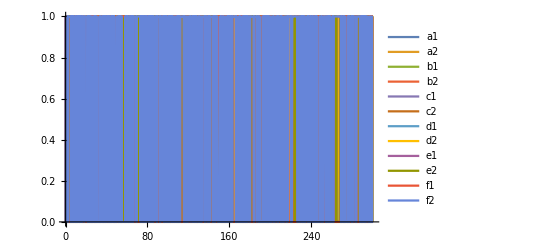

(a1 | a2 | b1 | b2 | c1 | c2 | d1 | d2 | e1 | e2 | f1 | f2
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0)

```mathematica
GraphColorSolution2[3,G2]
```

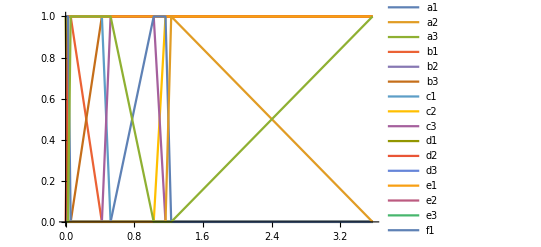

(a1 | a2 | a3 | b1 | b2 | b3 | c1 | c2 | c3 | d1 | d2 | d3 | e1 | e2 | e3 | f1 | f2 | f3
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1)

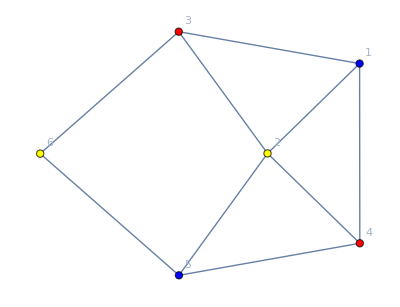

```mathematica
Graph[G2,VertexLabels->Automatic,VertexStyle->{1->Blue,2->Yellow,3->Red,4->Red,5->Blue,6->Yellow}]
```

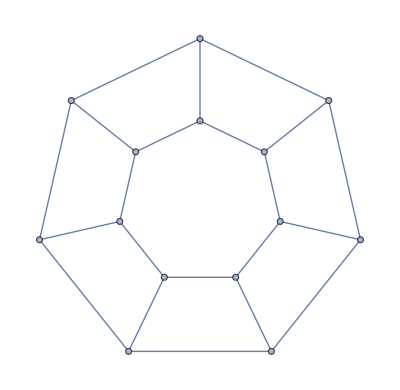

```mathematica
G3=PetersenGraph[7,6]
```

```mathematica
{VertexList[G3],EdgeList[G3]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1<->2,1<->7,1<->8,2<->3,2<->9,3<->4,3<->10,4<->5,4<->11,5<->6,5<->12,6<->7,6<->13,7<->14,8<->9,8<->14,9<->10,10<->11,11<->12,12<->13,13<->14}}

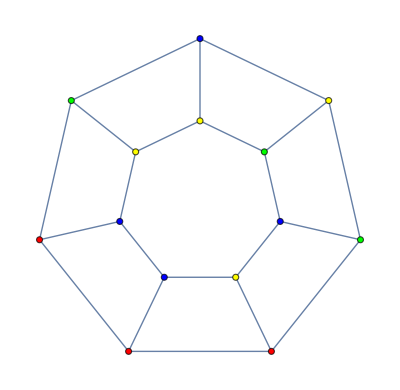

```mathematica
Graph[G3,VertexStyle->(MapThread[Rule,{Range[14],RandomChoice[{Red,Green,Blue,Yellow},14]}])]
```

```mathematica
GraphColorSolution2[2,G3]
```

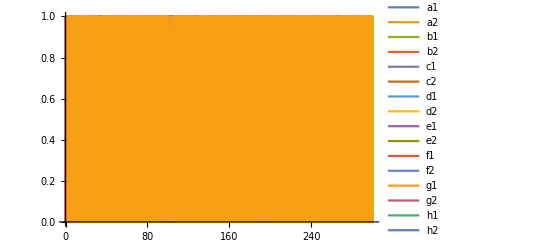

(a1 | a2 | b1 | b2 | c1 | c2 | d1 | d2 | e1 | e2 | f1 | f2 | g1 | g2 | h1 | h2 | i1 | i2 | j1 | j2 | k1 | k2 | l1 | l2 | m1 | m2 | n1 | n2
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1)

```mathematica
GraphColorSolution2[3,G3]
```

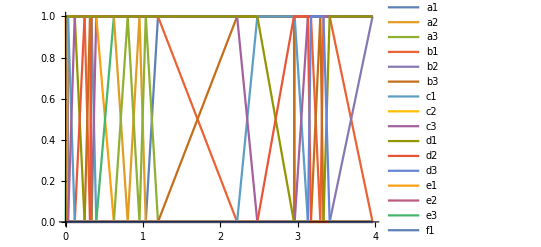

(a1 | a2 | a3 | b1 | b2 | b3 | c1 | c2 | c3 | d1 | d2 | d3 | e1 | e2 | e3 | f1 | f2 | f3 | g1 | g2 | g3 | h1 | h2 | h3 | i1 | i2 | i3 | j1 | j2 | j3 | k1 | k2 | k3 | l1 | l2 | l3 | m1 | m2 | m3 | n1 | n2 | n3
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

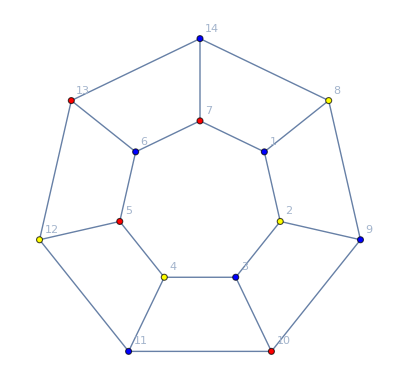

```mathematica
Graph[G3,VertexLabels->Automatic,VertexStyle->{1->Blue,2->Yellow,3->Blue,4->Yellow,5->Red,6->Blue,7-> Red,8-> Yellow,9->Blue,10->Red,11->Blue,12->Yellow,13->Red,14->Blue }]
```

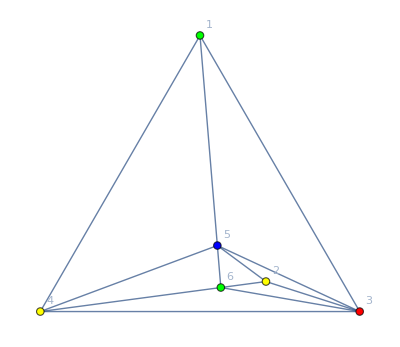

```mathematica
G4 = Graph[{1,2,3,4,5,6},{1<->4,1<->3,4<->3,5<->3,6<->3,4<->5,5<->6,2<->6,3<->2,4<->6,1<->5,2<->5}];
PlanarGraph[G4,VertexLabels->Automatic,VertexStyle->{1->Green,2->Yellow,3->Red,4->Yellow,5->Blue,6->Green}]
```

```mathematica
GraphColorSolution2[3,G4]
```

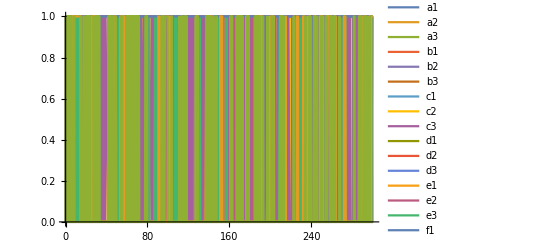

(a1 | a2 | a3 | b1 | b2 | b3 | c1 | c2 | c3 | d1 | d2 | d3 | e1 | e2 | e3 | f1 | f2 | f3
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
GraphColorSolution2[4,G4]
```

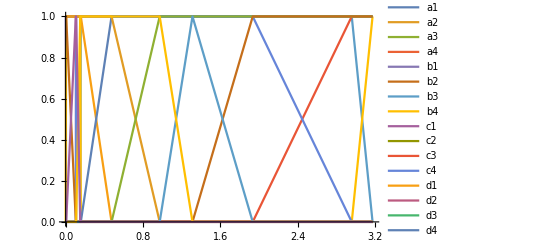

(a1 | a2 | a3 | a4 | b1 | b2 | b3 | b4 | c1 | c2 | c3 | c4 | d1 | d2 | d3 | d4 | e1 | e2 | e3 | e4 | f1 | f2 | f3 | f4
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
PlanarGraph[G4,VertexLabels->Automatic,VertexStyle->{1->Green,2->Yellow,3->Red,4->Yellow,5->Blue,6->Green}]
```

-Graphics-

(b).  Construct a single surface CRN that finds a 4-coloring for an arbitrary planar graph.   That is, the graph will be provided already encoded in the initial layout in a straightforward manner, and the surface CRN will eventually establish a color for each vertex and halt, with no more reactions possible.  We need to be clear about what we mean by “encoded in the initial layout” and “establish a color for each vertex”. 

Use the following encoding for the graphs:  Each vertex corresponds to a connected set of sites containing initial species “v”.   Each edge will consist of exactly 2 adjacent “e” sites, incident to each vertex region at exactly 1 site each, and not touching any other edge or vertex.  Unoccupied sites will be “w”.  Example layouts are given for G1, G2, G3, G4 from above.   To color a vertex region, the “v” species -- all of them! -- must be changed to a species indicating the color, e.g. “v[R]”, “v[G]”, “v[B]”, “v[Y]”, or if you prefer numbers, “v[1]”, “v[2]”, “v[3]”, “v[4]”.   For a valid coloring, all sites with a given vertex region must be the same color, neighboring vertex regions must have different colors, edge sites can be anything, and unoccupied sites must never change.  Your CRN may introduce additional species as necessary, so long as the system is guaranteed to eventually halt with a valid coloring.  

Relevant background: For planar graphs, the 3-color decision problem (“does there exist a valid 3-coloring?”) is NP-complete, so finding an actual solution is NP-hard, but the 4-color decision problem (“does there exist a valid 4-coloring?”) is trivial because in 1976 Appel & Haken proved that the answer is always “yes!”... but actually finding a valid 4-coloring can still be challenging (see e.g. Heuristics for Rapidly Four-Coloring Large Planar Graphs, Morgenstern & Shapiro, 1991).  The argument for the correctness of your surface CRN (which need not be efficient, just correct) may rely on the assumed correctness of Appel & Haken’s proof.

We will have reactions between adjacent vertex cells that are different colors to be the same color (reactions in both directions), so all cells in a vertex region will end up the same color. We will have reactions between adjacent vertex and edge cells that are different colors to be the same color (reactions in both directions), so edge regions will be split with each cell the color of the closest vertex. We will have reactions between adjacent edge cells that are the same colors to be different colors (reactions in both directions), so we cannot end with two vertex regions that are the same color.

```mathematica
Clear[w,v,V,e (* more species here *)];
```

```mathematica
k=4;
```

```mathematica
mapG1i={
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{e,w,v,v,v,e,e,v,v,v,e,e,v,v,v},
{e,w,v,v,v,w,w,v,v,v,w,w,v,v,v},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,e,w,w,w,w,e,w,w,w,w,e,w},
{v,w,w,v,w,w,w,v,v,v,w,w,w,v,w},
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,w}
};
```

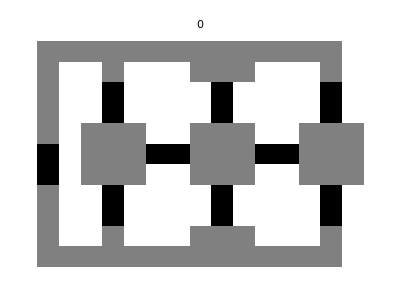

```mathematica
ArrayPlot[mapG1i,ColorRules->{w->White,v->Gray,e-> Black},PlotLabel->0]
```

```mathematica
Dynamic[ArrayPlot[mapG1,ColorRules->{w->White,v->Gray,e-> Black,e[1]->Red,e[2]->Blue,e[3]->Yellow,e[4]->Green,v[1]->Red,v[2]->Blue,v[3]->Yellow,v[4]->Green},PlotLabel->maptime]]
```

```mathematica
mapG1=mapG1i/.{v->v[1],e->e[1]};
coloring=Flatten[Table[Table[If[i==j,{rxno[e[i]+e[i],e[i]+e[Mod[i,k]+1],1],rxno[e[i]+e[i],e[i]+e[If[i==1,k,i-1]],1]},{rxno[v[i]+v[j],v[i]+v[i],1],rxno[v[i]+e[j],v[i]+e[i],1],rxno[v[i]+e[j],v[j]+e[j],1]}],{j,1,k}],{i,1,k}]];
time=0;
While[!HaltedSurfaceCRNQ[coloring,mapG1],mapG1=RunSurfaceCRN[coloring,mapG1,1];time+=1]
```

```mathematica
mapG2i={
{w,w,w,w,w,w,w,w,w,w,w,w,w,w},
{w,v,v,v,v,v,e,e,v,v,v,v,v,w},
{w,v,v,v,v,w,w,w,v,v,v,w,e,w},
{w,v,v,v,e,w,v,w,e,v,w,w,e,w},
{w,e,w,w,e,v,v,v,e,w,w,v,v,w},
{w,e,w,e,v,v,v,w,w,w,v,v,v,w},
{w,v,v,e,w,w,e,e,w,w,v,v,v,w},
{w,v,v,v,e,w,w,v,v,w,e,w,v,w},
{w,v,w,w,e,v,v,v,v,v,e,w,w,w},
{w,w,w,w,w,w,w,w,w,w,w,w,w,w}
};
```

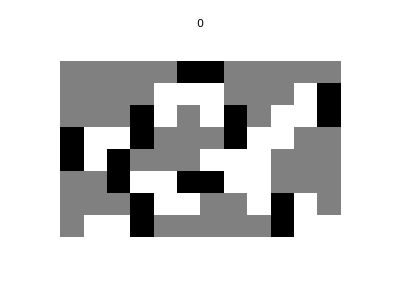

```mathematica
ArrayPlot[mapG2i,ColorRules->{w->White,v->Gray,e-> Black},PlotLabel->0]
```

```mathematica
Dynamic[ArrayPlot[mapG2,ColorRules->{w->White,v->Gray,e-> Black,e[1]->Red,e[2]->Blue,e[3]->Yellow,e[4]->Green,v[1]->Red,v[2]->Blue,v[3]->Yellow,v[4]->Green},PlotLabel->maptime]]
```

```mathematica
mapG2=mapG2i/.{v->v[1],e->e[1]};
coloring=Flatten[Table[Table[If[i==j,{rxno[e[i]+e[i],e[i]+e[Mod[i,k]+1],1],rxno[e[i]+e[i],e[i]+e[If[i==1,k,i-1]],1]},{rxno[v[i]+v[j],v[i]+v[i],1],rxno[v[i]+e[j],v[i]+e[i],1],rxno[v[i]+e[j],v[j]+e[j],1]}],{j,1,k}],{i,1,k}]];
time=0;
While[!HaltedSurfaceCRNQ[coloring,mapG2],mapG2=RunSurfaceCRN[coloring,mapG2,1];time+=1]
```

```mathematica
mapG3i={
{w,w,w,e,e,v,v,v,v,v,v,v,v,v,v,v,e,e,w,w,w},
{w,v,v,v,w,w,w,w,w,v,v,v,w,w,w,w,w,v,v,v,w},
{w,v,v,v,e,e,w,w,w,w,e,w,w,w,w,e,e,v,v,v,w},
{v,v,v,v,w,v,v,v,w,w,e,w,w,v,v,v,w,v,v,v,v},
{v,w,w,w,w,v,v,v,w,v,v,v,w,v,v,v,w,w,w,w,v},
{v,w,w,w,e,v,v,v,w,v,v,v,w,v,v,v,e,w,w,w,v},
{e,w,w,w,e,w,w,e,e,v,v,v,e,e,w,w,e,w,w,w,e},
{e,w,w,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,w,w,e},
{v,w,w,v,v,v,v,e,w,w,w,w,w,e,v,v,v,v,w,w,v},
{v,w,e,v,v,v,w,e,w,w,w,w,w,e,w,v,v,v,e,w,v},
{v,v,e,w,w,w,v,v,v,w,w,w,v,v,v,w,w,w,e,v,v},
{v,v,w,w,w,e,v,v,v,v,e,w,v,v,v,e,w,w,w,v,v},
{v,v,e,w,w,e,w,v,v,w,e,v,v,v,w,e,w,w,e,v,v},
{w,w,e,v,v,v,w,w,w,w,w,w,w,w,w,v,v,v,e,w,w},
{w,w,w,v,v,v,v,v,v,e,e,v,v,v,v,v,v,v,w,w,w}
};
```

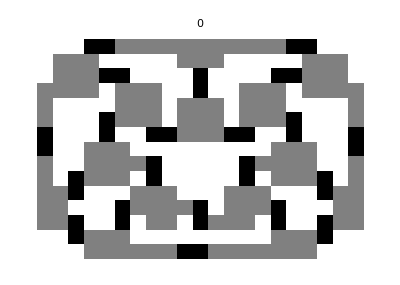

```mathematica
ArrayPlot[mapG3i,ColorRules->{w->White,v->Gray,e-> Black},PlotLabel->0]
```

```mathematica
Dynamic[ArrayPlot[mapG3,ColorRules->{w->White,v->Gray,e-> Black,e[1]->Red,e[2]->Blue,e[3]->Yellow,e[4]->Green,v[1]->Red,v[2]->Blue,v[3]->Yellow,v[4]->Green},PlotLabel->maptime]]
```

```mathematica
mapG3=mapG3i/.{v->v[1],e->e[1]};
coloring=Flatten[Table[Table[If[i==j,{rxno[e[i]+e[i],e[i]+e[Mod[i,k]+1],1],rxno[e[i]+e[i],e[i]+e[If[i==1,k,i-1]],1]},{rxno[v[i]+v[j],v[i]+v[i],1],rxno[v[i]+e[j],v[i]+e[i],1],rxno[v[i]+e[j],v[j]+e[j],1]}],{j,1,k}],{i,1,k}]];
time=0;
While[!HaltedSurfaceCRNQ[coloring,mapG3],mapG3=RunSurfaceCRN[coloring,mapG3,1];time+=1]
```

```mathematica
mapG4i={
{v,v,v,v,w,w,v,v,v,v,v,v,v,v,v },
{v,v,v,v,e,e,v,v,v,v,v,v,v,v,v},
{v,v,v,v,w,w,v,v,v,v,v,v,v,v,v},
{e,w,w,e,w,w,e,w,w,w,w,w,w,w,v},
{e,w,w,e,w,w,e,w,w,w,w,w,w,w,v},
{v,e,e,v,v,v,v,e,e,v,v,v,e,e,v},
{v,w,w,v,v,v,v,w,w,v,v,v,w,w,v},
{v,w,w,v,v,v,v,w,w,v,v,v,w,w,v},
{v,w,w,w,w,w,e,w,w,w,e,w,w,w,v},
{v,w,w,w,w,w,e,w,w,w,e,w,w,w,v},
{v,v,v,v,e,e,v,v,v,v,v,v,e,e,v},
{v,v,v,v,w,w,v,v,v,v,v,v,w,w,e},
{v,v,v,v,w,w,v,v,v,v,v,v,w,w,e},
{v,v,v,v,w,w,w,w,w,w,w,w,w,w,v},
{v,v,v,v,v,v,v,v,v,v,v,v,v,v,v}
};
```

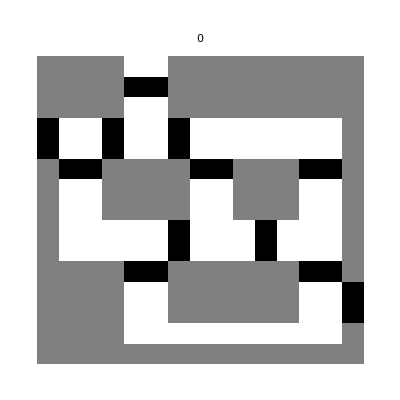

```mathematica
ArrayPlot[mapG4i,ColorRules->{w->White,v->Gray,e-> Black},PlotLabel->0]
```

```mathematica
Dynamic[ArrayPlot[mapG4,ColorRules->{w->White,v->Gray,e-> Black,e[1]->Red,e[2]->Blue,e[3]->Yellow,e[4]->Green,v[1]->Red,v[2]->Blue,v[3]->Yellow,v[4]->Green},PlotLabel->maptime]]
```

```mathematica
mapG4=mapG4i/.{v->v[1],e->e[1]};
coloring=Flatten[Table[Table[If[i==j,{rxno[e[i]+e[i],e[i]+e[Mod[i,k]+1],1],rxno[e[i]+e[i],e[i]+e[If[i==1,k,i-1]],1]},{rxno[v[i]+v[j],v[i]+v[i],1],rxno[v[i]+e[j],v[i]+e[i],1],rxno[v[i]+e[j],v[j]+e[j],1]}],{j,1,k}],{i,1,k}]];
time=0;
While[!HaltedSurfaceCRNQ[coloring,mapG4],mapG4=RunSurfaceCRN[coloring,mapG4,1];time+=1]
```

We can modify k to be 3 or 5 to solve for 3- or 5- coloring problems respectively. Non-planar graphs would be more trouble for the surface CRN as we would have to find a way to represent a non-planar graph in a surface CRN. If there is no valid coloring the CRN will run indefinitely as in part a. One issue with my CRN coloring solution is that it can take a while and not be very efficient as when a vertex is attempted to be colored a new color it takes a while sometimes doesn’t work because each cell in the vertex needs to be individually changed with a 50/50 chance. We could make this more efficient by having the vertices be colored easier and more quickly; a simple way would be to decrease the number of cells for each vertex but we could also try changing the reactions or increasing rates.

## Part 2: Open-ended exploration of pattern-formation by surface CRNs.

Design a surface CRN that, starting from a single S in a large field of EMPTY (or whatever you want to call it), robustly grows into a target pattern of your choice.  Maybe someone will choose a solid smiley face, another person will choose an outline of a smiley face, someone else will choose a tree-like shape, a fourth will make concentric rings, perhaps someone very advanced will get the S to grow into the outline and internal structure of a canonical Eukaryotic cell. I am envisioning the target pattern being a finite, fixed, exact, static pattern, such that it will turn out the same (up to orientation) in every run -- thus forcing you to grapple with the issue of reliability and robustness in asynchronous processes. If you decide instead to make a pattern that’s different in each run (such as a “tree”, but a different “tree” each time) or something that moves (like the wiggling “legs” of the “bug” in the notebook) then you must clearly define and describe the space of possibilities and explain why your construction doesn’t “break” and do something crazy, such as a tree branch growing forever or a leg breaking off and crawling away.  In addition to grappling with how to achieve a deterministic result with a stochastic model, also consider the extent to which your approach is exploiting the algorithmic potential of surface CRNs.  One  characteristic of algorithmic systems is that the size of the output, i.e. the constructed pattern, can be much greater than the size of the program, i.e. the number of CRN reactions.   I suggest that you explore approaches that are more inventive and “natural” than turn-the-crank Turing machine simulation, but it should be noted that the surface CRN ability to simulate Turing machines also enables them to act as universal programmable constructor: the input program tells the Turing machine what algorithm to execute in order to construct the output object of  interest.

Set a fixed amount of time to spend on this problem, and report just your favorite construction, whether it is simple or complex. For reference, compare the number of pixels in the final pattern vs the number of reactions in your program.   I will show some or all of the solutions later in class, so say whether you’d like your artwork to by signed with your name or listed as anonymous.

```mathematica
checkboard={rxno[R+s,R+B,1],rxno[B+s,B+R,1]};
surface=With[{N=20,M=20},Table[If[i==Ceiling[N/2]&&j==Ceiling[M/2],R,s],{i,1,N},{j,1,M}]];
time=0;
While[!HaltedSurfaceCRNQ[checkboard,surface],surface=RunSurfaceCRN[checkboard,surface,1];time+=1]
```

Working on these constructions, the hardest part was making a finite, fixed, exact, static pattern that turns up the same each run. I spent quite a bit playing around with the line drawer to try to get the probes to work for other purposes (single extended probe to try to turn etc. but was unable to get something that turned up the same each run). I got a really simple checkerboard pattern working but this was an infinite pattern. My chosen construction ended up being one that I had started with of concentric rings, but I made a few additions to make sure that it turned up the same every time. I did this by adding reactions to fix any mistakes that happen.

```mathematica
circles={rxno[R+s,R+B,1],rxno[R+G,R+B,1],rxno[B+s,B+P,1],rxno[B+L,B+P,1],rxno[P+s,P+G,1],rxno[P+Y,P+G,1],rxno[G+s,G+L,1],rxno[L+s,L+Y,1]};
surface=With[{N=20,M=20},Table[If[i==Ceiling[N/2]&&j==Ceiling[M/2],R,s],{i,1,N},{j,1,M}]];
time=0;
While[!HaltedSurfaceCRNQ[circles,surface],surface=RunSurfaceCRN[circles,surface,1];time+=1]
```

```mathematica
Dynamic[ArrayPlot[surface,ColorRules-> {s->GrayLevel[.9],R->Red,B->Black,P->Pink,G->Green,L->Blue,Y->Yellow,Q->Orange,U->Purple,W->Cyan,M->Magenta,T->Brown},PlotLabel->time]]
```